# Avni - Schiller’s Generalized Roche lobes

Author : Martin Horvat, Jun 2016

Ref : 
*Avni, Y. & Schiller, N., Generalized Roche potential for misaligned binary systems - Properties of the critical lobe,  Astrophysical Journal, Part 1, vol. 257, June 15, 1982, p. 703-714. Research supported by the U.S.-Israel Binational Science Foundation;

*J. F. Sepinsky, B. Willems, and V. Kaloger, Equipotential Surfaces and Lagrangian Points in Nonsynchronous, Eccentric Binary and Planetary Systems,The Astrophysical Journal, 660:1624–1635, 2007 May 10

## Defining potential

```mathematica
(* Generalized Roche/Kopal potential, Avni, eq.5 *)
```

```mathematica
Omega[x_,y_,z_,{q_,F_,d_,theta_}]=FullSimplify[
1/Sqrt[x^2+y^2+z^2]+
q(1/Sqrt[(x-d)^2+y^2+z^2]-x/d^2)+
1/2F^2(1+q)((x*Cos[theta]-z*Sin[theta])^2+y^2)
]
```

1/(√(x^2+y^2+z^2))+q (-x/d^2+1/(√((d-x)^2+y^2+z^2)))+1/2 F^2 (1+q) (y^2+(x Cos[theta]-z Sin[theta])^2)

```mathematica
(* Gradient of the potential *)
```

```mathematica
DOmega[x_,y_,z_,{q_,F_,d_,theta_}]=FullSimplify[-D[Omega[x,y,z,{q,F,d,theta}],{{x,y,z}}]]
```

{x/((x^2+y^2+z^2)^(3/2))-q (-1/d^2+(d-x)/(((d-x)^2+y^2+z^2)^(3/2)))-F^2 (1+q) Cos[theta] (x Cos[theta]-z Sin[theta]),-F^2 (1+q) y+y (q/(((d-x)^2+y^2+z^2)^(3/2))+1/((x^2+y^2+z^2)^(3/2))),(q z)/(((d-x)^2+y^2+z^2)^(3/2))+z/((x^2+y^2+z^2)^(3/2))+F^2 (1+q) Sin[theta] (x Cos[theta]-z Sin[theta])}

```mathematica
DDOmega[x_,y_,z_,{q_,F_,d_,theta_}]=FullSimplify[D[DOmega[x,y,z,{q,F,d,theta}],{{x,y,z}}]]
```

{{(q (-2 (d-x)^2+y^2+z^2))/(((d-x)^2+y^2+z^2)^(5/2))-(3 x^2)/((x^2+y^2+z^2)^(5/2))+1/((x^2+y^2+z^2)^(3/2))-F^2 (1+q) Cos[theta]^2,(3 q (d-x) y)/(((d-x)^2+y^2+z^2)^(5/2))-(3 x y)/((x^2+y^2+z^2)^(5/2)),(3 q (d-x) z)/(((d-x)^2+y^2+z^2)^(5/2))-(3 x z)/((x^2+y^2+z^2)^(5/2))+F^2 (1+q) Cos[theta] Sin[theta]},{y ((3 q (d-x))/(((d-x)^2+y^2+z^2)^(5/2))-(3 x)/((x^2+y^2+z^2)^(5/2))),-F^2 (1+q)+(q ((d-x)^2-2 y^2+z^2))/(((d-x)^2+y^2+z^2)^(5/2))+(x^2-2 y^2+z^2)/((x^2+y^2+z^2)^(5/2)),y (-(3 q z)/(((d-x)^2+y^2+z^2)^(5/2))-(3 z)/((x^2+y^2+z^2)^(5/2)))},{(3 q (d-x) z)/(((d-x)^2+y^2+z^2)^(5/2))-(3 x z)/((x^2+y^2+z^2)^(5/2))+F^2 (1+q) Cos[theta] Sin[theta],-(3 q y z)/(((d-x)^2+y^2+z^2)^(5/2))-(3 y z)/((x^2+y^2+z^2)^(5/2)),q/(((d-x)^2+y^2+z^2)^(3/2))+1/((x^2+y^2+z^2)^(3/2))+z^2 (-(3 q)/(((d-x)^2+y^2+z^2)^(5/2))-3/((x^2+y^2+z^2)^(5/2)))-F^2 (1+q) Sin[theta]^2}}

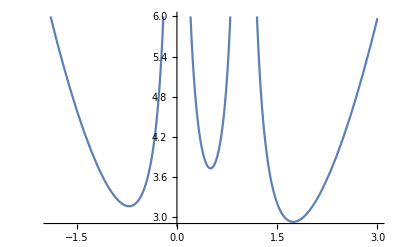

```mathematica
par={1,1,1,0.9Pi};
Plot[Omega[x,0,0,par],{x,-2,3},PlotRange->{All,{Automatic,6}}]
```

```mathematica
ContourPlot3D[
Omega[x,y,z,par]==3.5,
{x,-1,1.5},{y,-0.75,0.75},{z,-0.75,0.75},
PlotRange->All,
PlotPoints->30,
AxesLabel->{"x","y","z"},
AspectRatio->1
]
```

-Graphics3D-

```mathematica
(*X-Y*)
ContourPlot[
Omega[x,y,0.1,par],
{x,-2,2},
{y,-2,2},
Contours->100,
FrameLabel->{"x","y"}]
```

-Graphics-

```mathematica
(*X-Z*)
ContourPlot[
Omega[x,0.1,z,par],
{x,-2,2},
{z,-2,2},
Contours->100,
FrameLabel->{"x","z"}
]
```

-Graphics-